```mathematica
(*85microm exp1 video:7058*)
collateral85Exp1Top={0,0,0,0,0,1,1,0,1,0};
vCentral85Exp1={14,10,11,11,11,10,10,12,11,None};
collateral85Exp1Bottom={0,1,1,0,1,1,1,0,1,0};
nbGoutteCollateralTop85Exp1Top={2,3,3,3,2,3,3,2,3,2};
nbGoutteCentral85Exp1={2,3,3,2,2,2,2,2,3,1};
nbGoutteCollateralBottom85Exp1Bottom={3,3,3,2,2,3,3,1,3,3};

(*85microm exp2 video:7063*)
collateral85Exp2Top={1,1,0,0,1,1,1,1,1,0};
vCentral85Exp2={8,7,7,8,7,7,8,8,8,7};
collateral85Exp2Bottom={0,0,0,0,1,1,1,1,1,1};
nbGoutteCollateralTop85Exp2Top={3,3,3,3,3,3,3,3,3,3};
nbGoutteCentral85Exp2={3,3,3,3,3,3,3,3,3,3};
nbGoutteCollateralBottom85Exp2Bottom={3,3,3,3,3,3,3,3,3,3};

(*85microm exp3 video:7066*)
collateral85Exp3Top={0,0,0,0,0,0,0,0,0,0};
vCentral85Exp3={9,9,9,9,9,9,10,9,9,9};
collateral85Exp3Bottom={0,0,0,0,0,1,0,0,1,0};
nbGoutteCollateralTop85Exp3Top={2,2,1,2,1,2,2,2,2,2};
nbGoutteCentral85Exp3={2,2,2,2,2,2,2,2,2,2};
nbGoutteCollateralBottom85Exp3Bottom={1,1,2,2,2,2,2,2,2,1};

(*130microm exp1 video:7050*)
collateral130Exp1Top={0,1,0,0,0,0,0,0,0,0,0};
vCentral130Exp1={13,13,14,14,10,10,14,10,9,14,14};
collateral130Exp1Bottom={0,0,0,0,0,1,0,0,1,0,0};
nbGoutteCollateralTop130Exp1Top={2,3,2,2,2,2,2,2,3,2,2};
nbGoutteCentral130Exp1={2,2,2,2,3,3,2,3,3,2,2};
nbGoutteCollateralBottom130Exp1Bottom={2,2,2,2,3,3,2,2,3,2,2};

(*130microm exp2 video:7053*)
collateral130Exp2Top={0,0,1,1,1,1,1,1,0,1};
vCentral130Exp2={7,7,8,7,7,7,7,7,7,7};
collateral130Exp2Bottom={0,1,0,1,1,1,1,0,1,1};
nbGoutteCollateralTop130Exp2Top={2,2,3,3,3,3,3,3,2,3};
nbGoutteCentral130Exp2={3,3,2,3,2,3,3,3,3,3};
nbGoutteCollateralBottom130Exp2Bottom={3,3,3,3,3,3,3,2,3,3};

(*130microm exp3 video:7057*)
collateral130Exp3Top={0,0,0,0,0,0,0,0,0,0,0};
vCentral130Exp3={13,12,13,13,14,13,13,13,11,6,13};
collateral130Exp3Bottom={0,0,0,0,0,0,0,0,0,0,0};
nbGoutteCollateralTop130Exp3Top={2,2,2,2,2,2,2,2,2,3,2};
nbGoutteCentral130Exp3={2,2,2,2,2,2,2,2,2,2,2};
nbGoutteCollateralBottom130Exp3Bottom={3,2,2,2,2,2,2,2,3,2,2};
```

```mathematica
(*1. Fonction d'encodage adaptée aux cas à 1 seule goutte*)makeRawGrid[topColl_,topNDrops_,centerV_,centerNDrops_,botColl_,botNDrops_]:=Table[Module[{nDrop,vVal,mergedVal},Switch[i,1,(*Top*)nDrop=topNDrops[[j]];
mergedVal=If[nDrop>1,TrueQ[topColl[[j]]==1],Missing["SingleDroplet"]];
<|"N_drops"->nDrop,"Merged"->mergedVal|>,2,(*Center*)nDrop=centerNDrops[[j]];
vVal=centerV[[j]];
vVal=If[nDrop>1&&NumericQ[vVal],vVal,Missing["SingleDropletOrNoFusion"]];
<|"N_drops"->nDrop,"Voltage"->vVal|>,3,(*Bottom*)nDrop=botNDrops[[j]];
mergedVal=If[nDrop>1,TrueQ[botColl[[j]]==1],Missing["SingleDroplet"]];
<|"N_drops"->nDrop,"Merged"->mergedVal|>]],{i,1,3},{j,1,Length[centerV]}]

formatExperiment[coverslip_Integer,replicate_Integer,gridData_List]:=Module[{rows,cols},{rows,cols}=Dimensions[gridData];
Flatten@Table[Module[{puit=gridData[[i,j]],region,fuseV,mergedState},region=Switch[i,1,"Top",2,"Center",3,"Bottom"];
If[i==2,fuseV=puit["Voltage"];
mergedState=If[MissingQ[fuseV],Missing["SingleDropletOrNoFusion"],True];,fuseV=Missing["NotApplicable"];
mergedState=puit["Merged"];];
<|"Coverslip"->coverslip,"Replicate"->replicate,"Row"->i,"Col"->j,"Region"->region,"InitialDroplets"->puit["N_drops"],"FusionVoltage"->fuseV,"Merged"->mergedState|>],{i,1,rows},{j,1,cols}]]

(*2. Assemblage des 6 expériences*)
raw85Exp1=makeRawGrid[collateral85Exp1Top,nbGoutteCollateralTop85Exp1Top,vCentral85Exp1,nbGoutteCentral85Exp1,collateral85Exp1Bottom,nbGoutteCollateralBottom85Exp1Bottom];
raw85Exp2=makeRawGrid[collateral85Exp2Top,nbGoutteCollateralTop85Exp2Top,vCentral85Exp2,nbGoutteCentral85Exp2,collateral85Exp2Bottom,nbGoutteCollateralBottom85Exp2Bottom];
raw85Exp3=makeRawGrid[collateral85Exp3Top,nbGoutteCollateralTop85Exp3Top,vCentral85Exp3,nbGoutteCentral85Exp3,collateral85Exp3Bottom,nbGoutteCollateralBottom85Exp3Bottom];

raw130Exp1=makeRawGrid[collateral130Exp1Top,nbGoutteCollateralTop130Exp1Top,vCentral130Exp1,nbGoutteCentral130Exp1,collateral130Exp1Bottom,nbGoutteCollateralBottom130Exp1Bottom];
raw130Exp2=makeRawGrid[collateral130Exp2Top,nbGoutteCollateralTop130Exp2Top,vCentral130Exp2,nbGoutteCentral130Exp2,collateral130Exp2Bottom,nbGoutteCollateralBottom130Exp2Bottom];
raw130Exp3=makeRawGrid[collateral130Exp3Top,nbGoutteCollateralTop130Exp3Top,vCentral130Exp3,nbGoutteCentral130Exp3,collateral130Exp3Bottom,nbGoutteCollateralBottom130Exp3Bottom];

allDataList=Join[formatExperiment[85,1,raw85Exp1],formatExperiment[85,2,raw85Exp2],formatExperiment[85,3,raw85Exp3],formatExperiment[130,1,raw130Exp1],formatExperiment[130,2,raw130Exp2],formatExperiment[130,3,raw130Exp3]];

ds=Dataset[allDataList];
```

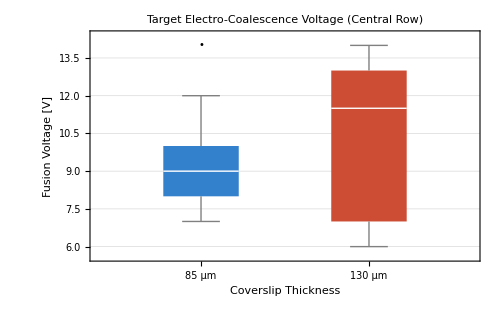

```mathematica
plotDataCentral=Normal@ds[Select[#Region=="Center"&&NumericQ[#FusionVoltage]&],{"Coverslip","Replicate","FusionVoltage"}];

plotCentral=BoxWhiskerChart[KeySort@GroupBy[plotDataCentral,#Coverslip&,#[[All,"FusionVoltage"]]&],"Outliers",ChartStyle->{RGBColor[0.2,0.5,0.8],RGBColor[0.8,0.3,0.2]},ChartLabels->{"85 μm","130 μm"},FrameLabel->{Style["Coverslip Thickness",12,Bold],Style["Fusion Voltage [V]",12,Bold]},PlotLabel->Style["Target Electro-Coalescence Voltage (Central Row)",14,Bold],GridLines->{None,Automatic},ImageSize->500]
```

```mathematica
(*Convertir le dataset en liste d'associations standard pour éviter les erreurs de typage Dataset*)listData=Normal[ds];

(*A.Analyse de la ligne centrale (Tensions de fusion) par réplicat*)
centerStats=Query[GroupBy[{#Coverslip,#Replicate}&],<|"N_valid"->Length,"Mean_V"->(Mean[#[[All,"FusionVoltage"]]]&),"Std_V"->(StandardDeviation[#[[All,"FusionVoltage"]]]&),"Min_V"->(Min[#[[All,"FusionVoltage"]]]&),"Max_V"->(Max[#[[All,"FusionVoltage"]]]&)|>]@Select[listData,#Region=="Center"&&NumericQ[#FusionVoltage]&]//Dataset

(*B.Analyse globale par épaisseur de coverslip (Ligne centrale)*)
centerGlobalStats=Query[GroupBy[#Coverslip&],<|"N_total"->Length,"Global_Mean_V"->(Mean[#[[All,"FusionVoltage"]]]&),"Global_Std_V"->(StandardDeviation[#[[All,"FusionVoltage"]]]&)|>]@Select[listData,#Region=="Center"&&NumericQ[#FusionVoltage]&]//Dataset

(*C.Taux de fusion collatérale (Lignes Top+Bottom,hors N_drops=1)*)
collateralStats=Query[GroupBy[#Coverslip&],<|"N_valid_wells"->Length,"N_collateral"->(Count[#[[All,"Merged"]],True]&),"Collateral_Probability"->(N[Count[#[[All,"Merged"]],True]/Length[#]]&)|>]@Select[listData,#Region!="Center"&&BooleanQ[#Merged]&]//Dataset
```

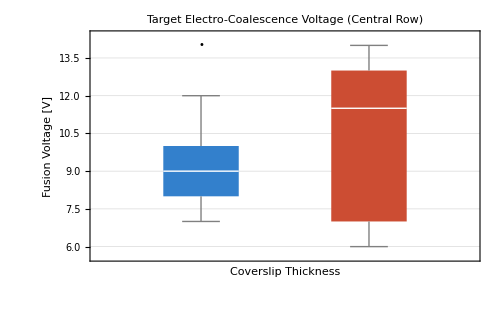

```mathematica
plotCentral=BoxWhiskerChart[<|"85 μm"->Select[centralDataForPlot,#Coverslip==85&][[All,"FusionVoltage"]],"130 μm"->Select[centralDataForPlot,#Coverslip==130&][[All,"FusionVoltage"]]|>,"Outliers",ChartStyle->{RGBColor[0.2,0.5,0.8],RGBColor[0.8,0.3,0.2]},Frame->True,FrameLabel->{Style["Coverslip Thickness",12,Bold],Style["Fusion Voltage [V]",12,Bold]},PlotLabel->Style["Target Electro-Coalescence Voltage (Central Row)",14,Bold],GridLines->{None,Automatic},ImageSize->500]
```

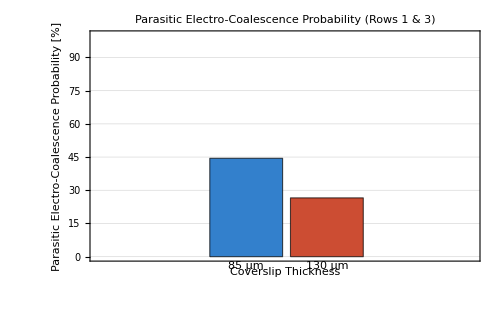

```mathematica
prob85=With[{sub=Select[sideDataForPlot,#Coverslip==85&]},100 Count[sub[[All,"Merged"]],True]/Length[sub]];

prob130=With[{sub=Select[sideDataForPlot,#Coverslip==130&]},100 Count[sub[[All,"Merged"]],True]/Length[sub]];

plotCollateral=BarChart[{prob85,prob130},ChartLabels->Placed[{"85 μm","130 μm"},Below],ChartStyle->{RGBColor[0.2,0.5,0.8],RGBColor[0.8,0.3,0.2]},Frame->True,FrameLabel->{Style["Coverslip Thickness",12,Bold],Style["Parasitic Electro-Coalescence Probability [%]",12,Bold]},PlotLabel->Style["Parasitic Electro-Coalescence Probability (Rows 1 & 3)",14,Bold],PlotRange->{0,100},GridLines->{None,Automatic},ImageSize->500]
```

```mathematica
(*85microm exp1 video:7058*)
collateral85Exp1Top={0,0,0,0,0,1,1,0,1,0};
vCentral85Exp1={14,10,11,11,11,10,10,12,11,None};
collateral85Exp1Bottom={0,1,1,0,1,1,1,0,1,0};
nbGoutteCollateralTop85Exp1Top={2,3,3,3,2,3,3,2,3,2};
nbGoutteCentral85Exp1={2,3,3,2,2,2,2,2,3,1};
nbGoutteCollateralBottom85Exp1Bottom={3,3,3,2,2,3,3,1,3,3};

(*85microm exp2 video:7063*)
collateral85Exp2Top={1,1,0,0,1,1,1,1,1,0};
vCentral85Exp2={8,7,7,8,7,7,8,8,8,7};
collateral85Exp2Bottom={0,0,0,0,1,1,1,1,1,1};
nbGoutteCollateralTop85Exp2Top={3,3,3,3,3,3,3,3,3,3};
nbGoutteCentral85Exp2={3,3,3,3,3,3,3,3,3,3};
nbGoutteCollateralBottom85Exp2Bottom={3,3,3,3,3,3,3,3,3,3};

(*85microm exp3 video:7066*)
collateral85Exp3Top={0,0,0,0,0,0,0,0,0,0};
vCentral85Exp3={9,9,9,9,9,9,10,9,9,9};
collateral85Exp3Bottom={0,0,0,0,0,1,0,0,1,0};
nbGoutteCollateralTop85Exp3Top={2,2,1,2,1,2,2,2,2,2};
nbGoutteCentral85Exp3={2,2,2,2,2,2,2,2,2,2};
nbGoutteCollateralBottom85Exp3Bottom={1,1,2,2,2,2,2,2,2,1};

(*130microm exp1 video:7050*)
collateral130Exp1Top={0,1,0,0,0,0,0,0,0,0,0};
vCentral130Exp1={13,13,14,14,10,10,14,10,9,14,14};
collateral130Exp1Bottom={0,0,0,0,0,1,0,0,1,0,0};
nbGoutteCollateralTop130Exp1Top={2,3,2,2,2,2,2,2,3,2,2};
nbGoutteCentral130Exp1={2,2,2,2,3,3,2,3,3,2,2};
nbGoutteCollateralBottom130Exp1Bottom={2,2,2,2,3,3,2,2,3,2,2};

(*130microm exp2 video:7053*)
collateral130Exp2Top={0,0,1,1,1,1,1,1,0,1};
vCentral130Exp2={7,7,8,7,7,7,7,7,7,7};
collateral130Exp2Bottom={0,1,0,1,1,1,1,0,1,1};
nbGoutteCollateralTop130Exp2Top={2,2,3,3,3,3,3,3,2,3};
nbGoutteCentral130Exp2={3,3,2,3,2,3,3,3,3,3};
nbGoutteCollateralBottom130Exp2Bottom={3,3,3,3,3,3,3,2,3,3};

(*130microm exp3 video:7057*)
collateral130Exp3Top={0,0,0,0,0,0,0,0,0,0,0};
vCentral130Exp3={13,12,13,13,14,13,13,13,11,6,13};
collateral130Exp3Bottom={0,0,0,0,0,0,0,0,0,0,0};
nbGoutteCollateralTop130Exp3Top={2,2,2,2,2,2,2,2,2,3,2};
nbGoutteCentral130Exp3={2,2,2,2,2,2,2,2,2,2,2};
nbGoutteCollateralBottom130Exp3Bottom={3,2,2,2,2,2,2,2,3,2,2};
```

```mathematica
(* ================================================================*)(*CONFIGURATION GRAPHIQUE*)(* ================================================================*)Needs["MaTeX`"];

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm}"}];

blue=RGBColor[0.2,0.5,0.8];
red=RGBColor[0.8,0.3,0.2];
```

Part::partw: Part 85 of <|{85,1}→{<|Coverslip→85,Replicate→1,Row→2,Col→1,Region→Center,InitialDroplets→2,FusionVoltage→14,Merged→True|>,«7»,<|Coverslip→85,Replicate→1,Row→2,Col→9,Region→Center,InitialDroplets→3,FusionVoltage→11,Merged→True|>},«4»,{130,3}→{<|«1»|>,«9»,<|«1»|>}|> does not exist.

Part::pspec1: Part specification FusionVoltage is not applicable.

Part::partw: Part 85 of <|{85,1}→{<|Coverslip→85,Replicate→1,Row→2,Col→1,Region→Center,InitialDroplets→2,FusionVoltage→14,Merged→True|>,«7»,<|Coverslip→85,Replicate→1,Row→2,Col→9,Region→Center,InitialDroplets→3,FusionVoltage→11,Merged→True|>},«4»,{130,3}→{<|«1»|>,«9»,<|«1»|>}|> does not exist.

Part::pspec1: Part specification FusionVoltage is not applicable.

Part::partw: Part 85 of <|{85,1}→{<|Coverslip→85,Replicate→1,Row→2,Col→1,Region→Center,InitialDroplets→2,FusionVoltage→14,Merged→True|>,«7»,<|Coverslip→85,Replicate→1,Row→2,Col→9,Region→Center,InitialDroplets→3,FusionVoltage→11,Merged→True|>},«4»,{130,3}→{<|«1»|>,«9»,<|«1»|>}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pspec1: Part specification FusionVoltage is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Part::partw: Part 85 of <|85→{<|Coverslip→85,Replicate→1,Row→2,Col→1,Region→Center,InitialDroplets→2,FusionVoltage→14,Merged→True|>,«27»,<|Coverslip→85,Replicate→3,Row→2,Col→10,Region→Center,InitialDroplets→2,FusionVoltage→9,Merged→True|>},130→{<|«1»|>,«30»,<|Coverslip→130,«7»|>}|> does not exist.

Part::pspec1: Part specification FusionVoltage is not applicable.

Part::partw: Part 130 of <|85→{<|Coverslip→85,Replicate→1,Row→2,Col→1,Region→Center,InitialDroplets→2,FusionVoltage→14,Merged→True|>,«27»,<|Coverslip→85,Replicate→3,Row→2,Col→10,Region→Center,InitialDroplets→2,FusionVoltage→9,Merged→True|>},130→{<|«1»|>,«30»,<|Coverslip→130,«7»|>}|> does not exist.

Part::pspec1: Part specification FusionVoltage is not applicable.

Part::partw: Part 85 of <|85→{<|Coverslip→85,Replicate→1,Row→1,Col→1,Region→Top,InitialDroplets→2,FusionVoltage→Missing[NotApplicable],Merged→False|>,«52»,<|Coverslip→85,Replicate→3,Row→3,Col→9,…→…,InitialDroplets→2,FusionVoltage→Missing[NotApplicable],Merged→True|>},130→«1»|> does not exist.

Part::pspec1: Part specification Merged is not applicable.

Part::partw: Part 130 of <|85→{<|Coverslip→85,Replicate→1,Row→1,Col→1,Region→Top,InitialDroplets→2,FusionVoltage→Missing[NotApplicable],Merged→False|>,«52»,<|Coverslip→85,Replicate→3,Row→3,Col→9,…→…,InitialDroplets→2,FusionVoltage→Missing[NotApplicable],Merged→True|>},130→«1»|> does not exist.

Part::pspec1: Part specification Merged is not applicable.

Coverslip [μm] | N valid wells | N parasitic fusions | Probability [%]
85 | 3 | 0 | 0.0
130 | 3 | 0 | 0.0

Coverslip | N | -Graphics- | -Graphics-
85 μm | 29 | 8.53 | 0.97
130 μm | 32 | 10.26 | 2.32

Coverslip | N | Mean [V] | Std [V] | Median [V] | Min [V] | Max [V] | -Graphics- | Parasitic fusion [%]
85 μm | 29 | 266/29 | √(1133/406) | 9 | 7 | 14 | 8.53 | 0.0
130 μm | 32 | 85/8 | √(543/62) | 23/2 | 6 | 14 | 10.26 | 0.0

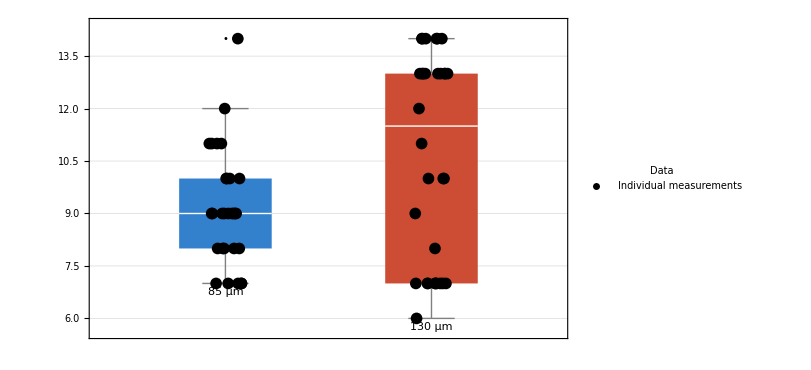

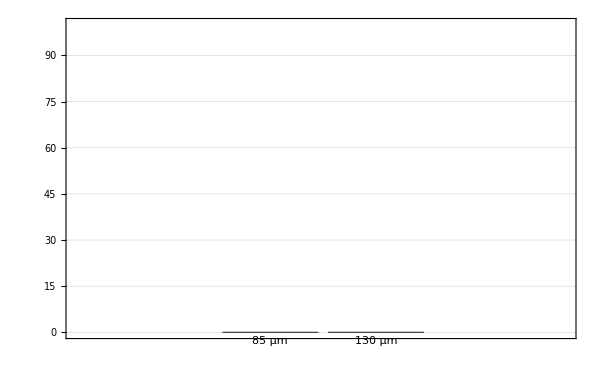

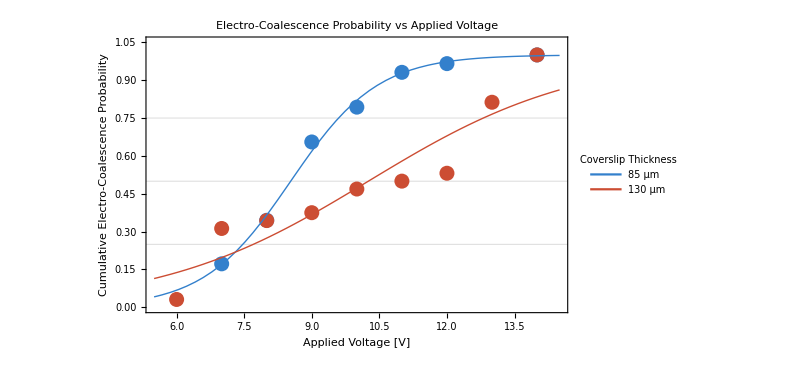

```mathematica
(* ================================================================*)(*ANALYSE COMPLETE DE L'ELECTRO-COALESCENCE*)(*Coverslips 85 µm et 130 µm*)(* ================================================================*)(* ================================================================*)(*1. ENCODAGE DES DONNEES*)(* ================================================================*)makeRawGrid[topColl_,topNDrops_,centerV_,centerNDrops_,botColl_,botNDrops_]:=Table[Module[{nDrop,vVal,mergedVal},Switch[i,(*----------------TOP----------------*)1,nDrop=topNDrops[[j]];
mergedVal=If[nDrop>1,TrueQ[topColl[[j]]==1],Missing["SingleDroplet"]];
<|"N_drops"->nDrop,"Merged"->mergedVal|>,(*---------------CENTER--------------*)2,nDrop=centerNDrops[[j]];
vVal=centerV[[j]];
vVal=If[nDrop>1&&NumericQ[vVal],vVal,Missing["SingleDropletOrNoFusion"]];
<|"N_drops"->nDrop,"Voltage"->vVal|>,(*---------------BOTTOM--------------*)3,nDrop=botNDrops[[j]];
mergedVal=If[nDrop>1,TrueQ[botColl[[j]]==1],Missing["SingleDroplet"]];
<|"N_drops"->nDrop,"Merged"->mergedVal|>]],{i,1,3},{j,1,Length[centerV]}];


formatExperiment[coverslip_Integer,replicate_Integer,gridData_List]:=Module[{rows,cols},{rows,cols}=Dimensions[gridData];
Flatten[Table[Module[{puit=gridData[[i,j]],region,fuseV,mergedState},region=Switch[i,1,"Top",2,"Center",3,"Bottom"];
If[i==2,fuseV=puit["Voltage"];
mergedState=If[MissingQ[fuseV],Missing["SingleDropletOrNoFusion"],True],fuseV=Missing["NotApplicable"];
mergedState=puit["Merged"];];
<|"Coverslip"->coverslip,"Replicate"->replicate,"Row"->i,"Col"->j,"Region"->region,"InitialDroplets"->puit["N_drops"],"FusionVoltage"->fuseV,"Merged"->mergedState|>],{i,1,rows},{j,1,cols}]]];


(* ================================================================*)
(*2. ASSEMBLAGE DES 6 EXPERIENCES*)
(* ================================================================*)

raw85Exp1=makeRawGrid[collateral85Exp1Top,nbGoutteCollateralTop85Exp1Top,vCentral85Exp1,nbGoutteCentral85Exp1,collateral85Exp1Bottom,nbGoutteCollateralBottom85Exp1Bottom];

raw85Exp2=makeRawGrid[collateral85Exp2Top,nbGoutteCollateralTop85Exp2Top,vCentral85Exp2,nbGoutteCentral85Exp2,collateral85Exp2Bottom,nbGoutteCollateralBottom85Exp2Bottom];

raw85Exp3=makeRawGrid[collateral85Exp3Top,nbGoutteCollateralTop85Exp3Top,vCentral85Exp3,nbGoutteCentral85Exp3,collateral85Exp3Bottom,nbGoutteCollateralBottom85Exp3Bottom];


raw130Exp1=makeRawGrid[collateral130Exp1Top,nbGoutteCollateralTop130Exp1Top,vCentral130Exp1,nbGoutteCentral130Exp1,collateral130Exp1Bottom,nbGoutteCollateralBottom130Exp1Bottom];

raw130Exp2=makeRawGrid[collateral130Exp2Top,nbGoutteCollateralTop130Exp2Top,vCentral130Exp2,nbGoutteCentral130Exp2,collateral130Exp2Bottom,nbGoutteCollateralBottom130Exp2Bottom];

raw130Exp3=makeRawGrid[collateral130Exp3Top,nbGoutteCollateralTop130Exp3Top,vCentral130Exp3,nbGoutteCentral130Exp3,collateral130Exp3Bottom,nbGoutteCollateralBottom130Exp3Bottom];


allDataList=Join[formatExperiment[85,1,raw85Exp1],formatExperiment[85,2,raw85Exp2],formatExperiment[85,3,raw85Exp3],formatExperiment[130,1,raw130Exp1],formatExperiment[130,2,raw130Exp2],formatExperiment[130,3,raw130Exp3]];


ds=Dataset[allDataList];

listData=Normal[ds];


(* ================================================================*)
(*3. EXTRACTION DES DONNEES CENTRALES ET COLLATERALES*)
(* ================================================================*)

centralDataForPlot=Select[listData,#Region=="Center"&&NumericQ[#FusionVoltage]&];


sideDataForPlot=Select[listData,#Region!="Center"&&BooleanQ[#Merged]&];


data85=Select[centralDataForPlot,#Coverslip==85&][[All,"FusionVoltage"]];


data130=Select[centralDataForPlot,#Coverslip==130&][[All,"FusionVoltage"]];


(* ================================================================*)(*STATISTIQUES PAR REPLICAT*)(* ================================================================*)centerStatsRaw=GroupBy[Select[listData,#Region=="Center"&&NumericQ[#FusionVoltage]&],{#Coverslip,#Replicate}&];


centerStatsTable=Table[With[{vals=centerStatsRaw[[key]][[All,"FusionVoltage"]]},{key[[1]],key[[2]],Length[vals],Mean[vals],StandardDeviation[vals],Min[vals],Max[vals]}],{key,Sort[Keys[centerStatsRaw]]}];

centerStatsDisplay=Grid[Prepend[centerStatsTable/. {{a_,b_,c_,d_,e_,f_,g_}:>{a,b,c,NumberForm[d,{6,2}],NumberForm[e,{6,2}],NumberForm[f,{6,2}],NumberForm[g,{6,2}]}},{"Coverslip [μm]","Replicate","N","Mean [V]","Std [V]","Min [V]","Max [V]"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];


(* ================================================================*)(*STATISTIQUES GLOBALES*)(* ================================================================*)centerGlobalRaw=GroupBy[Select[listData,#Region=="Center"&&NumericQ[#FusionVoltage]&],#Coverslip&];


centerGlobalTable=Table[With[{vals=centerGlobalRaw[[key]][[All,"FusionVoltage"]]},{key,Length[vals],Mean[vals],StandardDeviation[vals],Median[vals],Min[vals],Max[vals]}],{key,Sort[Keys[centerGlobalRaw]]}];


centerGlobalDisplay=Grid[Prepend[centerGlobalTable/. {{a_,b_,c_,d_,e_,f_,g_}:>{a,b,NumberForm[c,{6,2}],NumberForm[d,{6,2}],NumberForm[e,{6,2}],NumberForm[f,{6,2}],NumberForm[g,{6,2}]}},{"Coverslip [μm]","N","Mean [V]","Std [V]","Median [V]","Min [V]","Max [V]"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];

(* ================================================================*)(*FUSION PARASITE*)(* ================================================================*)collateralRaw=GroupBy[sideDataForPlot,#Coverslip&];


collateralTable=Table[With[{merged=collateralRaw[[key]][[All,"Merged"]]},{key,Length[merged],Count[merged,True],N[100 Count[merged,True]/Length[merged]]}],{key,Sort[Keys[collateralRaw]]}];


collateralDisplay=Grid[Prepend[collateralTable/. {{a_,b_,c_,d_}:>{a,b,c,NumberForm[d,{6,1}]}},{"Coverslip [μm]","N valid wells","N parasitic fusions","Probability [%]"}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];


(* ================================================================*)(*BOXPLOT+DONNEES INDIVIDUELLES*)(* ================================================================*)SeedRandom[1234];

jitter85=RandomReal[{-0.08,0.08},Length[data85]];

jitter130=RandomReal[{-0.08,0.08},Length[data130]];


pointData85=Transpose[{1+jitter85,data85}];


pointData130=Transpose[{2+jitter130,data130}];


boxPlotBase=BoxWhiskerChart[{data85,data130},"Outliers",ChartStyle->{blue,red},ChartLabels->Placed[{"85 μm","130 μm"},Below],Frame->True,FrameLabel->{MaTeX["\\text{Coverslip thickness}",FontSize->13],MaTeX["\\text{Fusion voltage }(V)",FontSize->13]},PlotLabel->MaTeX["\\text{Target Electro-Coalescence Voltage (Central Row)}",FontSize->14],GridLines->{None,Automatic},PlotRange->All,ImageSize->600,ImagePadding->{{65,20},{55,20}}];


pointOverlay=Graphics[{Black,PointSize[0.014],Point[pointData85],Point[pointData130]}];


plotCentral=Legended[Show[boxPlotBase,pointOverlay],Placed[PointLegend[{Directive[Black,PointSize[0.014]]},{"Individual measurements"},LegendLabel->Style["Data",11,Bold]],{0.82,0.20}]];


(* ================================================================*)(*PROBABILITE DE FUSION PARASITE*)(* ================================================================*)prob85=collateralTable[[1,4]];

prob130=collateralTable[[2,4]];


plotCollateral=BarChart[{prob85,prob130},ChartLabels->Placed[{"85 μm","130 μm"},Below],ChartStyle->{blue,red},Frame->True,FrameLabel->{None,MaTeX["\\text{Parasitic Electro-Coalescence Probability }(\\%)",FontSize->13]},PlotLabel->MaTeX["\\text{Parasitic Electro-Coalescence Probability (Rows 1 \\& 3)}",FontSize->14],PlotRange->{0,100},GridLines->{None,Automatic},ImageSize->600,ImagePadding->{{65,20},{65,25}}];


(* ================================================================*)(*CDF EMPIRIQUE*)(* ================================================================*)makeGroupedCDF[data_List]:=Module[{values,n},values=Sort[DeleteDuplicates[data]];
n=Length[data];
Table[{v,N[Count[data,x_/;x<=v]/n]},{v,values}]];


groupedCDF85=makeGroupedCDF[data85];
groupedCDF130=makeGroupedCDF[data130];


(* ================================================================*)
(*AJUSTEMENT SIGMOIDAL*)
(* ================================================================*)

Clear[logistic,V,V50,s];

logistic[V_,V50_,s_]:=1/(1+Exp[-(V-V50)/s]);


fit85=NonlinearModelFit[groupedCDF85,logistic[V,V50,s],{{V50,Median[data85]},{s,1}},V];


fit130=NonlinearModelFit[groupedCDF130,logistic[V,V50,s],{{V50,Median[data130]},{s,1}},V];


(* ================================================================*)
(*PARAMETRES DES SIGMOIDES*)
(* ================================================================*)

sigmoidStatsTable={{"85 μm",Length[data85],V50/. fit85["BestFitParameters"],s/. fit85["BestFitParameters"]},{"130 μm",Length[data130],V50/. fit130["BestFitParameters"],s/. fit130["BestFitParameters"]}};


sigmoidStatsDisplay=Grid[Prepend[sigmoidStatsTable/. {{a_,b_,c_,d_}:>{a,b,NumberForm[c,{6,2}],NumberForm[d,{6,2}]}},{"Coverslip","N",MaTeX["V_{50}\\;(V)",FontSize->12],MaTeX["s\\;(V)",FontSize->12]}],Frame->All,Alignment->Center,Spacings->{2,1},Background->{None,{Lighter[Gray,.9],White}}];

(* ================================================================*)(*GRAPHIQUE CDF+SIGMOIDES*)(* ================================================================*)vMin=Min[Join[data85,data130]]-0.5;

vMax=Max[Join[data85,data130]]+0.5;


plotCDFbase=Show[(*Données 85 µm*)ListPlot[groupedCDF85,PlotStyle->{blue,PointSize[0.018]}],(*Données 130 µm*)ListPlot[groupedCDF130,PlotStyle->{red,PointSize[0.018]}],(*Sigmoïde 85 µm*)Plot[Evaluate[fit85[V]],{V,vMin,vMax},PlotStyle->{blue,Thick}],(*Sigmoïde 130 µm*)Plot[Evaluate[fit130[V]],{V,vMin,vMax},PlotStyle->{red,Thick}],Frame->True,FrameLabel->{MaTeX["\\text{Applied voltage }(V)",FontSize->13],MaTeX["\\text{Cumulative electro-coalescence probability}",FontSize->13]},PlotRange->{{vMin,vMax},{0,1.05}},GridLines->{None,{0.25,0.50,0.75}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->650,ImagePadding->{{70,25},{60,25}}];


plotCDF=Legended[plotCDFbase,Placed[LineLegend[{Directive[blue,Thick],Directive[red,Thick]},{"85 μm","130 μm"},LegendLabel->MaTeX["\\text{Coverslip thickness}",FontSize->11]],{0.78,0.25}]];


(* ================================================================*)
(*10. REGROUPEMENT DES TENSIONS IDENTIQUES*)
(*     ->utile pour une représentation plus lisible*)
(* ================================================================*)

makeGroupedCDF[data_List]:=Module[{values,n},values=Sort[DeleteDuplicates[data]];
n=Length[data];
Table[{v,N[Count[data,x_/;x<=v]/n,5]},{v,values}]];


groupedCDF85=makeGroupedCDF[data85];
groupedCDF130=makeGroupedCDF[data130];


(* ================================================================*)
(*11. AJUSTEMENT SIGMOIDAL*)
(* ================================================================*)

(*Forme:P(V)=1/(1+Exp[-(V-V50)/s]) V50=tension donnant 50 % de probabilité de fusion s=largeur de transition*)


logistic[V_,V50_,s_]:=1/(1+Exp[-(V-V50)/s]);


(*Estimation initiale à partir de la médiane*)

initialV5085=Median[data85];
initialV50130=Median[data130];


fit85=NonlinearModelFit[groupedCDF85,logistic[V,V50,s],{{V50,initialV5085},{s,1}},V];


fit130=NonlinearModelFit[groupedCDF130,logistic[V,V50,s],{{V50,initialV50130},{s,1}},V];


(* ================================================================*)
(*12. EXTRACTION DE V50 ET DES PARAMETRES*)
(* ================================================================*)

sigmoidStats=Dataset[{<|"Coverslip"->"85 μm","N"->Length[data85],"V50 [V]"->N[V50/. fit85["BestFitParameters"],5],"s [V]"->N[s/. fit85["BestFitParameters"],5]|>,<|"Coverslip"->"130 μm","N"->Length[data130],"V50 [V]"->N[V50/. fit130["BestFitParameters"],5],"s [V]"->N[s/. fit130["BestFitParameters"],5]|>}];


(* ================================================================*)
(*13. GRAPHIQUE CDF+SIGMOIDES*)
(* ================================================================*)

vMin=Min[Join[data85,data130]]-0.5;


vMax=Max[Join[data85,data130]]+0.5;


plotCDF=Show[(*--------CDF expérimentale 85 µm--------*)ListPlot[groupedCDF85,PlotStyle->{blue,PointSize[0.018]},PlotLegends->None],(*--------CDF expérimentale 130 µm--------*)ListPlot[groupedCDF130,PlotStyle->{red,PointSize[0.018]},PlotLegends->None],(*--------Sigmoïde 85 µm--------*)Plot[Evaluate[fit85[V]],{V,vMin,vMax},PlotStyle->{blue,Thick}],(*--------Sigmoïde 130 µm--------*)Plot[Evaluate[fit130[V]],{V,vMin,vMax},PlotStyle->{red,Thick}],Frame->True,FrameLabel->{Style["Applied Voltage [V]",12,Bold],Style["Cumulative Electro-Coalescence Probability",12,Bold]},PlotLabel->Style["Electro-Coalescence Probability vs Applied Voltage",14,Bold],PlotRange->{{vMin,vMax},{0,1.05}},GridLines->{None,{0.25,0.5,0.75}},ImageSize->600,ImagePadding->{{65,20},{55,20}}];


plotCDF=Legended[plotCDF,Placed[LineLegend[{blue,red},{"85 μm","130 μm"},LegendLabel->Style["Coverslip Thickness",11,Bold]],{0.78,0.25}]];


(* ================================================================*)(*TABLEAU FINAL*)(* ================================================================*)finalSummaryTable={{"85 μm",Length[data85],Mean[data85],StandardDeviation[data85],Median[data85],Min[data85],Max[data85],V50/. fit85["BestFitParameters"],prob85},{"130 μm",Length[data130],Mean[data130],StandardDeviation[data130],Median[data130],Min[data130],Max[data130],V50/. fit130["BestFitParameters"],prob130}};


finalSummaryDisplay=Grid[Prepend[finalSummaryTable/. {{a_,b_,c_,d_,e_,f_,g_,h_,i_}:>{a,b,NumberForm[c,{6,2}],NumberForm[d,{6,2}],NumberForm[e,{6,2}],NumberForm[f,{6,2}],NumberForm[g,{6,2}],NumberForm[h,{6,2}],NumberForm[i,{6,1}]}},{"Coverslip","N","Mean [V]","Std [V]","Median [V]","Min [V]","Max [V]",MaTeX["V_{50}\\;(V)",FontSize->11],"Parasitic fusion [%]"}],Frame->All,Alignment->Center,Spacings->{1.5,1},Background->{None,{Lighter[Gray,.9],White}}];


(* ================================================================*)(*AFFICHAGE FINAL*)(* ================================================================*)centerStatsDisplay
centerGlobalDisplay
collateralDisplay
sigmoidStatsDisplay
finalSummaryDisplay

plotCentral
plotCollateral
plotCDF
```